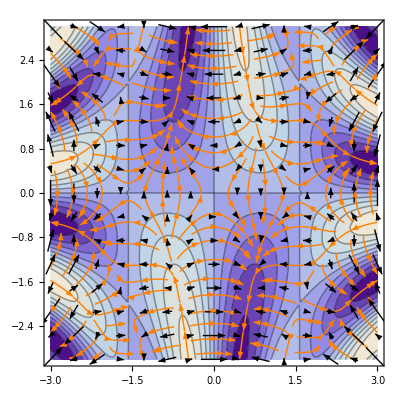

```mathematica
ClearAll["Global`*"]
(* ColorFunction->"LakeColors" is the Mathematica default *)
min=-3;
max=3;

(*surf[x_,y_]:=Sin[x]Sin[y];*)
surf[x_,y_]:=Sin[x y]Cos[x];
vx[x_,y_] = - D[surf[x,y],x];
vy[x_,y_] = - D[surf[x,y],y];

dp=DensityPlot[Sqrt[vx[x,y]^2+vy[x,y]^2],{x,min,max},{y,min,max}];
cp=ContourPlot[surf[x,y],{x,min,max},{y,min,max},ColorFunction->"LakeColors"];
vp =VectorPlot[{vx[x,y],vy[x,y]},{x,min,max},{y,min,max},VectorStyle->{Black}];
sp = StreamPlot[{vx[x,y],vy[x,y]},{x,min,max},{y,min,max},StreamStyle->Orange];
(*StreamDensityPlot[{vx[x,y],vy[x,y]},{x,min,max},{y,min,max}]*)(*VectorDensityPlot[{vx[x,y],vy[x,y]},{x,min,max},{y,min,max}]*)
(*GraphicsGrid[{{cp,dp},{vp,sp}}]*)
Show[cp,sp,vp]
```

```mathematica
(*colorfunction1=ColorData["LakeColors"]
OwnValues[colorfunction1]*)
```